```mathematica
(* Demonstration of the curse of dimensionality *)

Clear["Global`*"];
(* calculate time to collision with wall *)
WallTime[posA_, velA_, sigma_]:=Module[{delT},delT=1000000;

delT=If[velA>0.0,(1.0-sigma-posA)/velA,If[velA<0.0,(posA-sigma)/Abs[velA],Null]];
If[delT==Null,delT= 1000000];

delT
];
(* calculate time to collsion with particle *)
PairTime[posA_, velA_, posB_, velB_, sigma_]:=Module[{delT,delX,delX2,delV,delV2,scal,upsilon},delT=1000000;

delX={posB[[1]]-posA[[1]], posB[[2]]-posA[[2]]};
delV={velB[[1]]-velA[[1]], velB[[2]]-velA[[2]]};
delX2=delX[[1]]^2+delX[[2]]^2;
delV2=delV[[1]]^2+delV[[2]]^2;
scal=delX[[1]]*delV[[1]]+delX[[2]]*delV[[2]];
upsilon=scal^2-delV2*(delX2-4*sigma^2);
delT=If[upsilon>0.0 && scal <0.0,-1.0*(scal+Sqrt[upsilon])/delV2];
If[delT==Null,delT= 1000000];

delT
];

(* init positions and velocities for 4 particles *)
posi={{0.250001,0.25},{0.75,0.25},{0.25,0.75},{0.75,0.75}};
veli={{0.21,0.12},{0.71,0.18},{-0.23,-0.79},{0.78,0.1177}};
singles={{0+1,0+1},{0+1,1+1},{1+1,0+1},{1+1,1+1},{2+1,0+1},{2+1,1+1},{3+1,0+1},{3+1,1+1}};
pairs={{0+1,1+1},{0+1,2+1},{0+1,3+1},{1+1,2+1},{1+1,3+1},{2+1,3+1}};
(* disk radius, start time, number of events *)
sigma=0.15;
t=0.0;
nevents=100;
(* helper variables *)
wallTimes={};
pairTimes={};
x=0;
nextEvent=0;
ix1=Null;

deltaX=0;
deltaY=0;
absolX=0;
ePerpX=0;
ePerpY=0;
deltaVx=0;
deltaVy=0;
scala=0;
Post={};

(* Big event loop *)
For[j1=0,j1< nevents,j1++;wallTimes={};pairTimes={};
(* calculate time to next wall collision *)
For[j2=0,j2< 8,j2++;
x=WallTime[posi[[singles[[j2,1]],singles[[j2,2]] ]],veli[[singles[[j2,1]],singles[[j2,2]]]],sigma];
(* Print[t]; *)
AppendTo[ wallTimes,x];
];
(* calculate time to next particle-to-particle collision *)
For[j2=0,j2< 6,j2++;
x=PairTime[posi[[pairs[[j2,1]]]],veli[[pairs[[j2,1]]]],posi[[pairs[[j2,2]]]],veli[[pairs[[j2,2]]]],sigma];
AppendTo[ pairTimes,x];
];
(* find next event *)
nextEvent=Min[Join[wallTimes,pairTimes]];
t=t+nextEvent;
(*Print[t];*)
(* calculate positions at next event *)
For[j2=0,j2< 8,j2++;
x=WallTime[posi[[singles[[j2,1]],singles[[j2,2]] ]],veli[[singles[[j2,1]],singles[[j2,2]]]],sigma];
posi[[singles[[j2,1]],singles[[j2,2]]]]=posi[[singles[[j2,1]],singles[[j2,2]]]]+veli[[singles[[j2,1]],singles[[j2,2]]]]*nextEvent;
];
(* calculate change in velocity after collision *)
(* check if wall collision *)
ix1=Null;
If[Min[wallTimes]<Min[pairTimes],ix1=Position[wallTimes,nextEvent];
veli[[singles[[ix1[[1]][[1]],1]],singles[[ix1[[1]][[1]],2]]]]=veli[[singles[[ix1[[1]][[1]],1]],singles[[ix1[[1]][[1]],2]]]]*(-1.0);
];

(* check if particle to particle collision *) 
If[ix1==Null,ix1=Position[pairTimes,nextEvent];
deltaX=posi[[pairs[[ix1[[1]][[1]],2]],1]]-posi[[pairs[[ix1[[1]][[1]],1]],1]];
deltaY=posi[[pairs[[ix1[[1]][[1]],2]],2]]-posi[[pairs[[ix1[[1]][[1]],1]],2]];
absolX=Sqrt[deltaX^2+deltaY^2];
ePerpX=deltaX/absolX;
ePerpY=deltaY/absolX;
deltaVx=veli[[pairs[[ix1[[1]][[1]],2]],1]]-veli[[pairs[[ix1[[1]][[1]],1]],1]];
deltaVy=veli[[pairs[[ix1[[1]][[1]],2]],2]]-veli[[pairs[[ix1[[1]][[1]],1]],2]];
scala=deltaVx*ePerpX+deltaVy*ePerpY;
veli[[pairs[[ix1[[1]][[1]],1]],1]]=veli[[pairs[[ix1[[1]][[1]],1]],1]]+ePerpX*scala; (* particle A, x-direction change *)
veli[[pairs[[ix1[[1]][[1]],2]],1]]=veli[[pairs[[ix1[[1]][[1]],2]],1]]-ePerpX*scala; (* particle B, x-direction change *)
veli[[pairs[[ix1[[1]][[1]],1]],2]]=veli[[pairs[[ix1[[1]][[1]],1]],2]]+ePerpY*scala; (* particle A, y-direction change *)
veli[[pairs[[ix1[[1]][[1]],2]],2]]=veli[[pairs[[ix1[[1]][[1]],2]],2]]-ePerpY*scala;  (* particle B, y-direction change *)
];

(* Print["event:",j1, "  time: ", t," ; ",  posi]; *)
(* Print[veli]; *)
AppendTo[Post,posi];
];


Print["event:",j1, "  time: ", t," ; ",  posi]
```

event:100  time: 6.3601 ; {{0.721788,0.85},{0.837569,0.546793},{0.316979,0.427534},{0.166244,0.801061}}

```mathematica
Post[[100]]
```

{{0.721788,0.85},{0.837569,0.546793},{0.316979,0.427534},{0.166244,0.801061}}

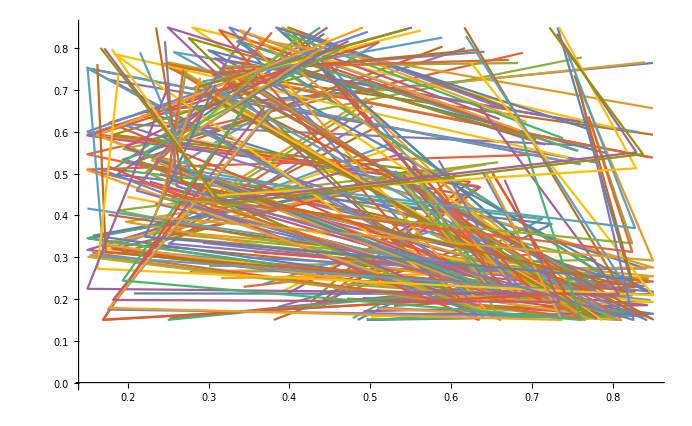

```mathematica
ListLinePlot[Post]
```